```mathematica
AppendTo[$Path,"~/projects/KnotTheory/trunk/"];
```

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of January 20, 2015, 10:42:19.1122.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
brace[l_]:=brace[0,l]
brace[k_,l_]:=w^k v^l+w^-k v^-l
bracket[k_,l_]:=w^k v^l-w^-k v^-l
```

```mathematica
dw=-(brace[2]bracket[1,5]bracket[1,-6])/(bracket[1,0]bracket[1,-1]);
```

```mathematica
Clear[i]
```

```mathematica
i[X_Times]:=i/@X
i[Power[X_,k_]]:=i[X]^k
i[n_Integer]:=n
```

```mathematica
i[1-x_]:=-i[x-1]
i[v]=v;
i[w]=w;
i[q]=q;
i[X_Plus]/;X⟦1⟧=!=1∧X⟦1⟧=!=-1:=X⟦1⟧i[Expand[X/X⟦1⟧]]
```

```mathematica
c[n_,z_]:=
With[{a=Exponent[z,v],b=Exponent[z,w]},
Product[(PowerExpand[(v^a w^b)^(n/(2d))]brk[(n b)/(2 d),(n a)/(2d)])^MoebiusMu[d],{d,Divisors[n]}]
]
```

```mathematica
cq[n_]:=
Product[(q^(n/(2d))qi[n/(2d)])^MoebiusMu[d],{d,Divisors[n]}]
```

```mathematica
Do[i[Cyclotomic[n,z]]=c[n,z],{n,1,20},{z,DeleteCases[Flatten[Table[v^k w^l,{k,-12,12},{l,-6,6}]],1]}];
```

```mathematica
Do[i[Cyclotomic[n,z]]=c[n,z],{n,1,20},{z,DeleteCases[Table[v^k,{k,-50,50}],1]}];
```

```mathematica
Do[i[Cyclotomic[n,q]]=cq[n],{n,1,100}]
```

KnotTheory::loading: Loading precomputed data in PD4Knots`.

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

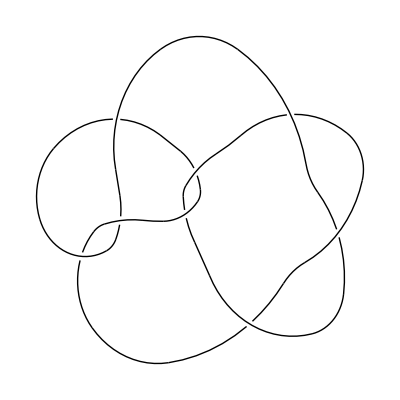

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
Writhe[k:(_Knot|_Link|_BR)]:=Writhe[PD[k]]
Writhe[p_PD]:=With[{o=OPD[p]},Count[o,_Xp]-Count[o,_Xn]]
```

```mathematica
RotateBox[X_,0]:=X
RotateBox[RotateBox[X_,k_],l_]:=RotateBox[X,k+l]
```

```mathematica
ClearAll[PlanarDiagram]
```

```mathematica
SetAttributes[PlanarDiagram,{Flat,Orderless,OneIdentity}]
```

```mathematica
PlanarDiagram[Box[{a_,a_,b___},X_]]:=PlanarDiagram[Box[{b},Stitch[X]]]
PlanarDiagram[Box[{a__,b_,b_,c___},X_]]:=PlanarDiagram[Box[{b,b,c,a},RotateBox[X,Length[{a}]]]]
```

```mathematica
PlanarDiagram[Box[{b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a_,b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{a,b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a___,b_,c_,d___},X_],Box[{e___,c_,b_,f___},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,f,e},RotateBox[Y,Length[{e}]]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{d___,a_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,e,d},RotateBox[Y,Length[{d}]]]]
PlanarDiagram[Box[{a___,b_,c_,d__},X_],Box[{b_,e___,c_},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,e},RotateBox[Y,-1]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{c_,d___,a_},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,d},RotateBox[Y,-1]]]
```

```mathematica
PlanarDiagram[Box[{a___,b_,c___},X_],Box[{d___,b_,e___},Y_]]:=PlanarDiagram[Box[{c,a,e,d},Multiply[1][RotateBox[X,-Length[{c}]],RotateBox[Y,Length[{d}]]]]]
```

```mathematica
PlanarDiagram[p_PD]:=PlanarDiagram@@(p/.{X[a_,b_,c_,d_]:>Box[{c,d,a,b},X],Y[a_,b_,c_]:>Box[{a,b,c},Y]})
```

```mathematica
PlanarDiagram[K:(_Knot|_Link)]:=Module[{result},
result=Quiet[PlanarDiagram[PD[K]],$IterationLimit::itlim];
If[FreeQ[result,Hold],
PlanarDiagram[K]=result,
$Failed]
]
```

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][X,Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-1]],1]]],1]]]]]

```mathematica
Cases[AllKnots[{3,11}],K_/;PlanarDiagram[K]⟦1,1⟧≠{}]
```

KnotTheory::loading: Loading precomputed data in DTCode4KnotsTo11`.

KnotTheory::credits: The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005.

{}

```mathematica
(*Cases[AllKnots[12],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]==={Knot[12,Alternating,1251]}*)
```

```mathematica
(*Cases[AllKnots[13],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

```mathematica
(*Cases[AllKnots[14],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

```mathematica
(*Cases[AllKnots[15],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

```mathematica
(*Cases[AllKnots[16],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]*)
```

KnotTheory::loading: Loading precomputed data in KnotTheory/12A.dts.

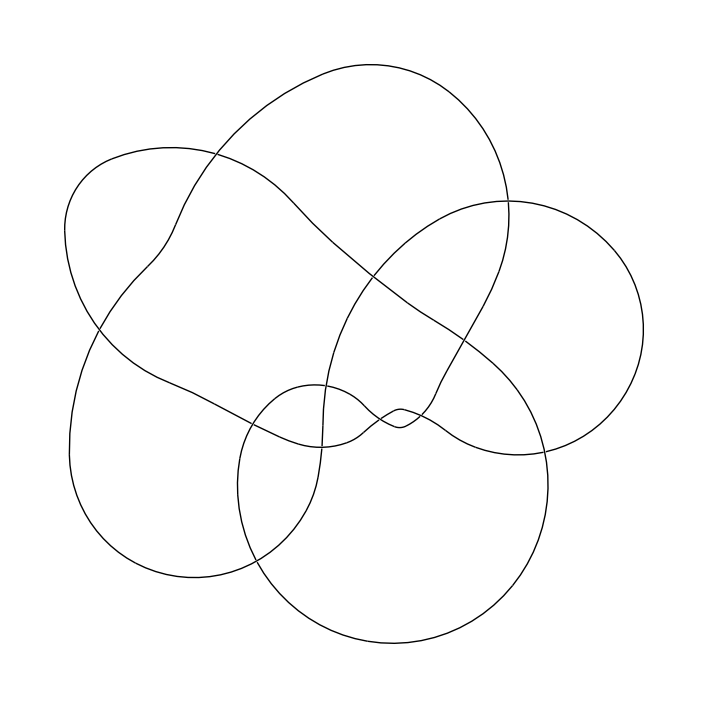

```mathematica
DrawPD[Knot[12,Alternating,1251]]
```

### Loading matrices

```mathematica
Clear[QESRotation,QESBraiding,QESInverseBraiding,QESCupCap,QESCap,QESCup,QESI,QESH,QESFork,QESFuse]
```

```mathematica
ZeroMatrix[n_]:=Table[0,{n},{n}]
ZeroMatrix[n_,m_]:=Table[0,{n},{m}]
```

```mathematica
QESDimension[n_]:=Length[QESRotation[n]]
```

```mathematica
QESId[n_]:=IdentityMatrix[QESDimension[n]]
QESZero[n_,m_]:=ZeroMatrix[QESDimension[n],QESDimension[m]]
QESRotation[0]:={{1}}
QESRotation[1]:={}
QESRotation[n_]:=QESRotation[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-rotation-matrix.m"}]];
QESRotation[n_,k_]/;k<0∨k≥n:=QESRotation[n,Mod[k,n]]
QESRotation[n_,0]:=IdentityMatrix[Length[QESRotation[n]]]
QESRotation[n_,1]:=QESRotation[n]
QESRotation[n_,k_]:=QESRotation[n,k]=Together[QESRotation[n].QESRotation[n,k-1]]
QESBraiding[n_]:=QESBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-braiding-matrix.m"}]];
QESBraiding[n_,k_]:=QESBraiding[n,k]=Together[QESRotation[n,-k].QESBraiding[n].QESRotation[n,k]]
QESInverseBraiding[n_]:=QESInverseBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-inverse-braiding-matrix.m"}]];
QESInverseBraiding[n_,k_]:=QESInverseBraiding[n,k]=Together[QESRotation[n,-k].QESInverseBraiding[n].QESRotation[n,k]]
QESCupCap[n_]:=QESCupCap[n]=Together[QESCup[n-2].QESCap[n]]
QESCupCap[3]={{0}};
QESCup[0]={{1}};
QESCup[1]={{}};
QESCup[n_]:=QESCup[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cup-matrix.m"}]]
QESCap[2]={{d}};
QESCap[n_]:=QESCap[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cap-matrix.m"}]]
QESI[n_]:=QESI[n]=Together[QESFork[n-1].QESFuse[n]]
QESFork[n_]:=QESFork[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fork-matrix.m"}]]
QESFuse[n_]:=QESFuse[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fuse-matrix.m"}]]
QESH[n_]:=QESH[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-H-matrix.m"}]]
```

### Verifying matrices

```mathematica
Table[Together[QESRotation[k,k-1].QESRotation[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESCupCap[k].QESCupCap[k]==d QESCupCap[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESFuse[k+2].QESCup[k]==QESZero[k+1,k],{k,1,4}]
```

{True,True,True,True}

```mathematica
Table[Together[QESBraiding[k].QESInverseBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[Together[QESInverseBraiding[k].QESBraiding[k]]==QESId[k],{k,2,6}]
```

{True,True,True,True,True}

```mathematica
Table[QESBraiding[k+1].QESFork[k]==(-v^6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESInverseBraiding[k+1].QESFork[k]==(-v^-6)QESFork[k],{k,2,5}]
```

{True,True,True,True}

```mathematica
Table[QESBraiding[k+2].QESCup[k]==(v^12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
Table[QESInverseBraiding[k+2].QESCup[k]==(v^-12)QESCup[k],{k,2,4}]
```

{True,True,True}

```mathematica
(*Table[Together[QESBraiding[k,0].QESBraiding[k,1].QESBraiding[k,0]-QESBraiding[k,1].QESBraiding[k,0].QESBraiding[k,1]]==QESZero[k],{k,2,6}]*)
```

```mathematica
(* There's still lots more interesting stuff that could be verified here. *)
```

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESCupCap[k]/.d->dw],{k,2,6}]]]]
```

-(v^33 w^4 brk[0,1] brk[0,3] brk[0,6] brk[1,-1] brk[1,0] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^2)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESI[k],{k,3,6}]]]
```

v^18 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^3

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESI[k]/.d->dw],{k,3,6}]]]]
```

(v^40 w^2 brk[0,3]^2 brk[0,6] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^3)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESH[k],{k,3,6}]]]
```

v^16 (1+v^2) (1-v+v^2)^2 (1+v+v^2)^2 (1+v^4)^2 (1+d v^2+v^4) (1+d v^8+v^16)^4

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESH[k]/.d->dw],{k,3,6}]]]]
```

(v^48 w^2 brk[0,1] brk[0,3]^3 brk[0,6] i[1+w^2/v^6+v^4 w^2+w^4/v^2]^4)/brk[0,2]

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESBraiding[k],{k,3,6}]]]
```

v^24 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

```mathematica
i[PolynomialLCM@@Denominator[Flatten[Table[Together[QESBraiding[k]/.d->dw],{k,3,6}]]]]
```

(v^43 w^4 brk[0,1]^2 brk[0,3] brk[0,6]^2 i[1+w^2/v^6+v^4 w^2+w^4/v^2]^3)/brk[0,2]^2

```mathematica
PolynomialLCM@@Denominator[Flatten[Table[QESInverseBraiding[k],{k,3,6}]]]
```

v^30 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^2+v^4)^2 (1+d v^8+v^16)^3

### Stuff

```mathematica
RotateBox[QESBox[n_][v_],k_]:=QESBox[n][Together[QESRotation[n,k].v]]
```

```mathematica
Stitch[QESBox[n_][v_]]:=QESBox[n-2][Together[QESCap[n].v]]
Stitch[QESBox[3][v_]]:=QESBox[1][{}]
```

```mathematica
AddStrand[QESBox[n_][v_]]:=QESBox[n+2][Together[QESCup[n].v]]
```

```mathematica
Multiply[2][QESBox[4][w_],QESBox[n_][v_]]:=QESBox[n][Together[Together[w.{QESCupCap[n],IdentityMatrix[Length[v]],QESI[n],QESH[n],QESBraiding[n]}].v]]
```

```mathematica
Multiply[2][QESBox[3][w_],QESBox[n_][v_]]:=QESBox[n-1][Together[Together[w.{QESFuse[n]}].v]]
```

```mathematica
Multiply[1][b1:QESBox[n1_][w_],b2:QESBox[n2_][v_]]:=Multiply[2][b1,RotateBox[AddStrand[RotateBox[b2,1]],-1]]
```

```mathematica
Multiply[1][QESBox[4][{1,0,0,0,0}],QESBox[4][{1,0,0,0,0}]]
```

QESBox[6][{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]

```mathematica
PlanarDiagram[unlink=PD[X[1,3,2,4],X[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[X,1],RotateBox[X,-2]],1]]]]]

```mathematica
OPD[PD[crossings___]]:=OPD[crossings]/.{X[i_,j_,k_,l_]/;(j-l==1||l-j>1):>Xp[i,j,k,l],X[i_,j_,k_,l_]/;(l-j==1||j-l>1):>Xn[i,j,k,l]}
```

```mathematica
OPD[K_Knot]:=OPD[PD[K]]
OPD[L_Link]:=OPD[PD[L]]
```

```mathematica
PD[OPD[f___]]:=Module[{pairs,rules,n=0,cycles},
pairs = Unordered@@(Join@@({f}/.{Xp[i_,j_,k_,l_]:>{{i,k},{l,j}},Xn[i_,j_,k_,l_]:>{{i,k},{j,l}}}));
cycles=List@@(pairs//.Unordered[{x___,y_},{y_,z___}]:>Unordered[{x,y,z}]);
rules=#->++n&/@Flatten[cycles];
PD[f]/.rules/.{Xp|Xn->X}
]
```

```mathematica
Clear[QESInvariant]
```

```mathematica
QESInvariant[K:(_Knot|_Link|_PD|_OPD)]:=v^(-12 Writhe[K])QESInvariant[PlanarDiagram[K]]
QESInvariant[planarDiagram_PlanarDiagram]:=QESInvariant[planarDiagram]=(planarDiagram/.{X->QESBox[4][QESBraiding[4]⟦All,2⟧],Y->QESBox[3][{1}]})/.PlanarDiagram[Box[{},QESBox[0][{z_}]]]:>Together[z]
```

```mathematica
timesToList[X_Times]:=List@@X
timesToList[X_]:={X}
```

```mathematica
Φ[brk[0,k_]]:=Product[Φ[d],{d,Cases[Divisors[k],d_/;Mod[d,4]≠2]}]
```

```mathematica
QESInvariantΦ[K_]:=Times@@(timesToList[i[Factor[QESInvariant[K]/.d->dw]]]/.i[t_]:>Collect[t,w,i[Factor[#]]&]/.i[t_]:>t/.brk[0,k_]:>Φ[brk[0,k]])
```

```mathematica
i41=Factor[QESInvariant[PD[Knot[4,1]]]/.d->dw]
```

-1/(v^36 (v-w) (-1+w) w^6 (1+w) (v+w))(1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (v^16-v^26-v^28+v^38+v^4 w^2-v^8 w^2+v^12 w^2-2 v^14 w^2-2 v^16 w^2+2 v^18 w^2+v^20 w^2-2 v^22 w^2+4 v^26 w^2-2 v^30 w^2+v^32 w^2+2 v^34 w^2-2 v^36 w^2-2 v^38 w^2+v^40 w^2-v^44 w^2+v^48 w^2-v^2 w^4-v^4 w^4+2 v^6 w^4-3 v^10 w^4+v^12 w^4+6 v^14 w^4-v^16 w^4-5 v^18 w^4+3 v^20 w^4+5 v^22 w^4-6 v^24 w^4-6 v^26 w^4+5 v^28 w^4+3 v^30 w^4-5 v^32 w^4-v^34 w^4+6 v^36 w^4+v^38 w^4-3 v^40 w^4+2 v^44 w^4-v^46 w^4-v^48 w^4+w^6+2 v^2 w^6-v^4 w^6-2 v^6 w^6+2 v^8 w^6+2 v^10 w^6-6 v^12 w^6-4 v^14 w^6+7 v^16 w^6+2 v^18 w^6-8 v^20 w^6+11 v^24 w^6-8 v^28 w^6+2 v^30 w^6+7 v^32 w^6-4 v^34 w^6-6 v^36 w^6+2 v^38 w^6+2 v^40 w^6-2 v^42 w^6-v^44 w^6+2 v^46 w^6+v^48 w^6-w^8-v^2 w^8+2 v^4 w^8-3 v^8 w^8+v^10 w^8+6 v^12 w^8-v^14 w^8-5 v^16 w^8+3 v^18 w^8+5 v^20 w^8-6 v^22 w^8-6 v^24 w^8+5 v^26 w^8+3 v^28 w^8-5 v^30 w^8-v^32 w^8+6 v^34 w^8+v^36 w^8-3 v^38 w^8+2 v^42 w^8-v^44 w^8-v^46 w^8+w^10-v^4 w^10+v^8 w^10-2 v^10 w^10-2 v^12 w^10+2 v^14 w^10+v^16 w^10-2 v^18 w^10+4 v^22 w^10-2 v^26 w^10+v^28 w^10+2 v^30 w^10-2 v^32 w^10-2 v^34 w^10+v^36 w^10-v^40 w^10+v^44 w^10+v^10 w^12-v^20 w^12-v^22 w^12+v^32 w^12)

```mathematica
Factor[(i41/.w->v/w)-i41]
```

0

```mathematica
qi[q_,m_]:=Sum[q^k,{k,-m+1,m-1,2}]
```

```mathematica
Factor[QESInvariant[PD[Knot[3,1]]]/.d->dw]
```

1/((v-w) (-1+w) w^4 (1+w) (v+w))v^12 (1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8)

```mathematica
Collect[1/w^4(-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8),w,Collect[#,v]&]
```

-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36+(-v^4+v^14+v^16-v^26)/w^4+(-v^6+v^10-v^14+v^16+v^18-v^20-v^22+v^24+v^26-v^28+v^32-v^36)/w^2+(-v^4+v^8-v^12+v^14+v^16-v^18-v^20+v^22+v^24-v^26+v^30-v^34) w^2+(-1+v^10+v^12-v^22) w^4

```mathematica
(w^4+v^4 w^-4)(-1+v^10+v^12-v^22)+(w^2+v^2 w^-2)(-v^4+v^8-v^12+v^14+v^16-v^18-v^20+v^22+v^24-v^26+v^30-v^34)+(-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36)//TeXForm
```

v^{36}+v^{34}-v^{32}+v^{28}-3 v^{24}-v^{22}+2 v^{20}-v^{16}+v^{14}+2 v^{12}-v^8-v^2+\left(-v^{22}+v^{12}+v^{10}-1\right)
   \left(\frac{v^4}{w^4}+w^4\right)+\left(-v^{34}+v^{30}-v^{26}+v^{24}+v^{22}-v^{20}-v^{18}+v^{16}+v^{14}-v^{12}+v^8-v^4\right) \left(\frac{v^2}{w^2}+w^2\right)-1

```mathematica
QESInvariantΦ[PD[Knot[4,1]]]
```

-1/(v^8 w^6 brk[1,-1] brk[1,0])brk[1,-6] brk[1,5] Φ[4] (((1+2 v^2-v^4-2 v^6+2 v^8+2 v^10-6 v^12-4 v^14+7 v^16+2 v^18-8 v^20+11 v^24-8 v^28+2 v^30+7 v^32-4 v^34-6 v^36+2 v^38+2 v^40-2 v^42-v^44+2 v^46+v^48) w^6)/v^16+v^11 Φ[1]^2 Φ[3] Φ[5]-((1+v^2-2 v^4+3 v^8-4 v^12+3 v^16-2 v^20+v^22+v^24) w^4 Φ[1]^2 Φ[3] Φ[5])/v^3-((1+v^2-2 v^4+3 v^8-4 v^12+3 v^16-2 v^20+v^22+v^24) w^8 Φ[1]^2 Φ[3] Φ[5])/v^5+v^5 w^12 Φ[1]^2 Φ[3] Φ[5]+v^10 w^2 Φ[1]^4 Φ[3] Φ[5]^2 Φ[8]+v^6 w^10 Φ[1]^4 Φ[3] Φ[5]^2 Φ[8])

```mathematica
Cyclotomic[5,x]
```

1+x+x^2+x^3+x^4

```mathematica
Φv[k_]/;OddQ[k]:=v^(-EulerPhi[k])Cyclotomic[k,v]Cyclotomic[2k,v]
Φv[k_]/;Mod[k,4]==0:=v^(-EulerPhi[k]/2)Cyclotomic[k,v]
```

```mathematica
Collect[Φv[5],v]
```

1+1/v^4+1/v^2+v^2+v^4

```mathematica
Collect[Φv[4],v]
```

1/v+v

```mathematica
QESInvariant[PD[ArcPresentation[{3,5},{6,4},{5,2},{1,3},{2,6},{4,1}]]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
(*DeleteFile[FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]]*)
```

```mathematica
With[{file=FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]},
If[FileExistsQ[file],
DownValues[QESInvariant]=Get[file]~Join~DownValues[QESInvariant]
]
];
```

```mathematica
QESInvariant[unlink]
```

d^2 v^24

```mathematica
QESInvariant[Knot[3,1]]
```

-1/((1+d v^2+v^4)^2)d v^4 (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+5 d v^28-2 d^2 v^28-2 v^30-d^2 v^30+v^34-6 d v^34+2 d^2 v^34+v^36-5 d v^36+2 d^2 v^36+3 v^38-6 d v^38+2 d^2 v^38+v^40-5 d v^40+2 d^2 v^40+v^42+2 d v^42-v^44-v^46+6 d v^46-2 d^2 v^46-6 v^48+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74)

```mathematica
Factor[%/.d->dw]
```

1/((v-w) (-1+w) w^4 (1+w) (v+w))v^12 (1+v^4) (v^6-w) (v^6+w) (-1+v^5 w) (1+v^5 w) (-v^4+v^14+v^16-v^26-v^6 w^2+v^10 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2+v^26 w^2-v^28 w^2+v^32 w^2-v^36 w^2-w^4-v^2 w^4-v^8 w^4+2 v^12 w^4+v^14 w^4-v^16 w^4+2 v^20 w^4-v^22 w^4-3 v^24 w^4+v^28 w^4-v^32 w^4+v^34 w^4+v^36 w^4-v^4 w^6+v^8 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6+v^24 w^6-v^26 w^6+v^30 w^6-v^34 w^6-w^8+v^10 w^8+v^12 w^8-v^22 w^8)

```mathematica
i[%]
```

-1/(w^4 brk[0,2] brk[1,-1] brk[1,0])v^28 brk[0,4] brk[1,-6] brk[1,5] i[1-v^10-v^12+v^22+v^2 w^2-v^6 w^2+v^10 w^2-v^12 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2-v^28 w^2+v^32 w^2+w^4/v^4+w^4/v^2+v^4 w^4-2 v^8 w^4-v^10 w^4+v^12 w^4-2 v^16 w^4+v^18 w^4+3 v^20 w^4-v^24 w^4+v^28 w^4-v^30 w^4-v^32 w^4+w^6-v^4 w^6+v^8 w^6-v^10 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6-v^26 w^6+v^30 w^6+w^8/v^4-v^6 w^8-v^8 w^8+v^18 w^8]

```mathematica
Collect[(1/(v^8 w^4))(1-v^10-v^12+v^22+v^2 w^2-v^6 w^2+v^10 w^2-v^12 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2-v^28 w^2+v^32 w^2+w^4/v^4+w^4/v^2+v^4 w^4-2 v^8 w^4-v^10 w^4+v^12 w^4-2 v^16 w^4+v^18 w^4+3 v^20 w^4-v^24 w^4+v^28 w^4-v^30 w^4-v^32 w^4+w^6-v^4 w^6+v^8 w^6-v^10 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6-v^26 w^6+v^30 w^6+w^8/v^4-v^6 w^8-v^8 w^8+v^18 w^8),w,Factor]
```

-(-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36)/v^12+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4))/(v^8 w^4)+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) (1-v^4+v^8))/(v^6 w^2)+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) (1-v^4+v^8) w^2)/v^8+((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) w^4)/v^12

```mathematica
Φ[brk[0,12]]
```

Φ[1] Φ[3] Φ[4] Φ[12]

```mathematica
Collect[(1/(v^8 w^4))(1-v^10-v^12+v^22+v^2 w^2-v^6 w^2+v^10 w^2-v^12 w^2-v^14 w^2+v^16 w^2+v^18 w^2-v^20 w^2-v^22 w^2+v^24 w^2-v^28 w^2+v^32 w^2+w^4/v^4+w^4/v^2+v^4 w^4-2 v^8 w^4-v^10 w^4+v^12 w^4-2 v^16 w^4+v^18 w^4+3 v^20 w^4-v^24 w^4+v^28 w^4-v^30 w^4-v^32 w^4+w^6-v^4 w^6+v^8 w^6-v^10 w^6-v^12 w^6+v^14 w^6+v^16 w^6-v^18 w^6-v^20 w^6+v^22 w^6-v^26 w^6+v^30 w^6+w^8/v^4-v^6 w^8-v^8 w^8+v^18 w^8),w,i[Factor[#]]/.brk[0,k_]:>Φ[brk[0,k]]&]
```

-i[-1-v^2-v^8+2 v^12+v^14-v^16+2 v^20-v^22-3 v^24+v^28-v^32+v^34+v^36]/v^12+(v^3 Φ[1]^2 Φ[3] Φ[5])/w^4+(w^4 Φ[1]^2 Φ[3] Φ[5])/v+(v^9 Φ[1]^2 Φ[3] Φ[5] Φ[12])/w^2+v^7 w^2 Φ[1]^2 Φ[3] Φ[5] Φ[12]

```mathematica
QESInvariant[Knot[4,1]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
QESInvariant[Knot[8,19]]
```

1/(v^70 (1+d v^2+v^4)^6)d (1-v^2+5 v^4-d v^4-5 v^6-d v^6+10 v^8-3 d v^8-11 v^10-4 d v^10+d^2 v^10+10 v^12+4 d v^12-14 v^14-5 d v^14+3 d^2 v^14+4 v^16+25 d v^16-6 d^2 v^16-9 v^18-2 d v^18-5 d^2 v^18-3 v^20+36 d v^20-22 d^2 v^20+d^3 v^20+5 v^22-7 d v^22-18 d^2 v^22+4 d^3 v^22-3 v^24+5 d v^24-14 d^2 v^24+7 d^3 v^24+21 v^26-2 d v^26+6 d^2 v^26+8 d^3 v^26+11 v^28-67 d v^28+72 d^2 v^28-4 d^3 v^28+28 v^30+62 d v^30+62 d^2 v^30-8 d^3 v^30+29 v^32-110 d v^32+165 d^2 v^32-50 d^3 v^32+9 d^4 v^32+19 v^34+160 d v^34+77 d^2 v^34-42 d^3 v^34+10 d^4 v^34+d^5 v^34+26 v^36-60 d v^36+62 d^2 v^36-31 d^3 v^36+21 d^4 v^36-7 v^38+205 d v^38-6 d^2 v^38-13 d^3 v^38+20 d^4 v^38-3 v^40+22 d v^40-203 d^2 v^40+138 d^3 v^40-8 d^4 v^40-39 v^42+139 d v^42-131 d^2 v^42+136 d^3 v^42-28 d^4 v^42-28 v^44+29 d v^44-285 d^2 v^44+275 d^3 v^44-83 d^4 v^44+4 d^5 v^44-50 v^46-34 d v^46-88 d^2 v^46+200 d^3 v^46-109 d^4 v^46+10 d^5 v^46-24 v^48-38 d v^48+16 d^2 v^48+79 d^3 v^48-82 d^4 v^48+9 d^5 v^48-21 v^50-244 d v^50+153 d^2 v^50-70 d^3 v^50-39 d^4 v^50+12 d^5 v^50-d^6 v^50-7 v^52-63 d v^52+447 d^2 v^52-407 d^3 v^52+116 d^4 v^52-11 d^5 v^52+22 v^54-356 d v^54+248 d^2 v^54-429 d^3 v^54+220 d^4 v^54-28 d^5 v^54-5 v^56+21 d v^56+488 d^2 v^56-620 d^3 v^56+331 d^4 v^56-55 d^5 v^56+2 d^6 v^56+31 v^58-239 d v^58-126 d^2 v^58-304 d^3 v^58+330 d^4 v^58-73 d^5 v^58+4 d^6 v^58-20 v^60+159 d v^60+18 d^2 v^60-89 d^3 v^60+135 d^4 v^60-40 d^5 v^60+3 d^6 v^60+7 v^62+23 d v^62-732 d^2 v^62+410 d^3 v^62-31 d^4 v^62-19 d^5 v^62+3 d^6 v^62-36 v^64+237 d v^64-488 d^2 v^64+729 d^3 v^64-432 d^4 v^64+91 d^5 v^64-5 d^6 v^64-5 v^66+161 d v^66-812 d^2 v^66+932 d^3 v^66-561 d^4 v^66+133 d^5 v^66-8 d^6 v^66-37 v^68+124 d v^68-450 d^2 v^68+805 d^3 v^68-680 d^4 v^68+196 d^5 v^68-15 d^6 v^68+9 v^70+60 d v^70-54 d^2 v^70+376 d^3 v^70-482 d^4 v^70+163 d^5 v^70-14 d^6 v^70-16 v^72-165 d v^72+153 d^2 v^72-195 d^3 v^72-106 d^4 v^72+71 d^5 v^72-7 d^6 v^72+19 v^74-92 d v^74+927 d^2 v^74-866 d^3 v^74+312 d^4 v^74-58 d^5 v^74+5 d^6 v^74+13 v^76-376 d v^76+562 d^2 v^76-1261 d^3 v^76+816 d^4 v^76-216 d^5 v^76+19 d^6 v^76+7 v^78-54 d v^78+1153 d^2 v^78-1357 d^3 v^78+870 d^4 v^78-270 d^5 v^78+27 d^6 v^78+24 v^80-270 d v^80+136 d^2 v^80-1020 d^3 v^80+957 d^4 v^80-315 d^5 v^80+31 d^6 v^80-14 v^82+162 d v^82+334 d^2 v^82-326 d^3 v^82+349 d^4 v^82-153 d^5 v^82+16 d^6 v^82+15 v^84+38 d v^84-799 d^2 v^84+458 d^3 v^84+5 d^4 v^84-53 d^5 v^84+5 d^6 v^84-29 v^86+314 d v^86-661 d^2 v^86+1203 d^3 v^86-760 d^4 v^86+180 d^5 v^86-17 d^6 v^86+9 v^88+204 d v^88-1167 d^2 v^88+1619 d^3 v^88-997 d^4 v^88+258 d^5 v^88-25 d^6 v^88-29 v^90+182 d v^90-772 d^2 v^90+1422 d^3 v^90-1079 d^4 v^90+308 d^5 v^90-30 d^6 v^90+15 v^92+106 d v^92-385 d^2 v^92+1104 d^3 v^92-870 d^4 v^92+243 d^5 v^92-23 d^6 v^92-9 v^94-161 d v^94+48 d^2 v^94+37 d^3 v^94-190 d^4 v^94+80 d^5 v^94-10 d^6 v^94+20 v^96-52 d v^96+861 d^2 v^96-613 d^3 v^96+200 d^4 v^96-28 d^5 v^96-d^6 v^96+18 v^98-380 d v^98+729 d^2 v^98-1414 d^3 v^98+848 d^4 v^98-182 d^5 v^98+10 d^6 v^98+14 v^100-26 d v^100+1350 d^2 v^100-1597 d^3 v^100+863 d^4 v^100-189 d^5 v^100+11 d^6 v^100+29 v^102-261 d v^102+432 d^2 v^102-1331 d^3 v^102+900 d^4 v^102-198 d^5 v^102+11 d^6 v^102-v^104+182 d v^104+617 d^2 v^104-818 d^3 v^104+444 d^4 v^104-92 d^5 v^104+5 d^6 v^104+21 v^106+28 d v^106-490 d^2 v^106+132 d^3 v^106+100 d^4 v^106-43 d^5 v^106+5 d^6 v^106-19 v^108+333 d v^108-512 d^2 v^108+693 d^3 v^108-321 d^4 v^108+47 d^5 v^108+13 v^110+154 d v^110-1002 d^2 v^110+1280 d^3 v^110-520 d^4 v^110+67 d^5 v^110-29 v^112+220 d v^112-918 d^2 v^112+1199 d^3 v^112-509 d^4 v^112+67 d^5 v^112+16 v^114+44 d v^114-511 d^2 v^114+980 d^3 v^114-422 d^4 v^114+55 d^5 v^114-20 v^116-89 d v^116-344 d^2 v^116+410 d^3 v^116-153 d^4 v^116+25 d^5 v^116+19 v^118-85 d v^118+474 d^2 v^118-162 d^3 v^118-3 d^4 v^118+15 d^5 v^118-2 v^120-317 d v^120+437 d^2 v^120-478 d^3 v^120+148 d^4 v^120+10 v^122-52 d v^122+971 d^2 v^122-778 d^3 v^122+185 d^4 v^122+3 v^124-277 d v^124+554 d^2 v^124-551 d^3 v^124+151 d^4 v^124-4 v^126+110 d v^126+570 d^2 v^126-475 d^3 v^126+115 d^4 v^126-4 v^128-47 d v^128+51 d^2 v^128-72 d^3 v^128+45 d^4 v^128-8 v^130+246 d v^130-178 d^2 v^130+60 d^3 v^130+25 d^4 v^130-3 v^132+143 d v^132-377 d^2 v^132+229 d^3 v^132+217 d v^134-488 d^2 v^134+240 d^3 v^134+11 v^136+156 d v^136-308 d^2 v^136+175 d^3 v^136+9 v^138+21 d v^138-244 d^2 v^138+130 d^3 v^138+24 v^140+46 d v^140+4 d^2 v^140+45 d^3 v^140+9 v^142-175 d v^142+94 d^2 v^142+25 d^3 v^142+25 v^144-39 d v^144+155 d^2 v^144-v^146-202 d v^146+175 d^2 v^146+15 v^148-24 d v^148+105 d^2 v^148-14 v^150-76 d v^150+85 d^2 v^150+v^152+35 d v^152+25 d^2 v^152-19 v^154+43 d v^154+16 d^2 v^154-9 v^156+55 d v^156-9 v^158+64 d v^158-10 v^160+30 d v^160+9 v^162+31 d v^162-5 v^164+6 d v^164+19 v^166+6 d v^166-v^168+15 v^170+6 v^174+v^178)

```mathematica
i/@Factor[(QESInvariant[PlanarDiagram[Box[{1,2,3,4},RotateBox[X,1]]]]/.d->dw)⟦1,2,1⟧]
```

{-(brk[0,2] brk[0,3] brk[1,-1] brk[1,0])/brk[0,6],(brk[0,2] brk[0,3] brk[1,-1] brk[1,0])/brk[0,6],(brk[0,2] brk[0,3]^2 brk[2,-6] brk[2,4])/(brk[0,1] brk[0,6] brk[1,-3] brk[1,2]),-(brk[0,2] brk[0,3]^2 brk[2,-6] brk[2,4])/(brk[0,1] brk[0,6] brk[1,-3] brk[1,2]),1}

```mathematica
%brk[0,6]/(brk[0,2]brk[0,3])
```

{-brk[1,-1] brk[1,0],brk[1,-1] brk[1,0],(brk[0,3] brk[2,-6] brk[2,4])/(brk[0,1] brk[1,-3] brk[1,2]),-(brk[0,3] brk[2,-6] brk[2,4])/(brk[0,1] brk[1,-3] brk[1,2]),brk[0,6]/(brk[0,2] brk[0,3])}

### Comparisons with A2 and G2

```mathematica
Quiet[<<QuantumGroups`]
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
AdjointRepresentation[Subscript[A, n_]]:=Irrep[Subscript[A, n]][UnitVector[n,1]+UnitVector[n,n]]
AdjointRepresentation[D4]=Irrep[D4][{0,1,0,0}];
AdjointRepresentation[G2]=Irrep[G2][UnitVector[2,2]];
AdjointRepresentation[F4]=Irrep[F4][UnitVector[4,1]];
AdjointRepresentation[E6]=Irrep[E6][UnitVector[6,2]];
AdjointRepresentation[E7]=Irrep[E7][UnitVector[7,1]];
AdjointRepresentation[E8]=Irrep[E8][UnitVector[8,8]];
```

```mathematica
qDimension[G2][AdjointRepresentation[G2]]
```

2+1/q^18+1/q^12+1/q^10+1/q^8+1/q^6+1/q^2+q^2+q^6+q^8+q^10+q^12+q^18

```mathematica
TwistFactor[Γ_,Irrep[Γ_][λ_]]:=q^(KillingForm[Γ][λ,λ+2ρ[Γ]])
```

```mathematica
QESSubstitution[Γ_,V_]/;Length[DecomposeRepresentation[Γ][V⊗V]]≤5:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
QESSubstitution[Γ_]:=QESSubstitution[Γ,AdjointRepresentation[Γ]]
```

```mathematica
QESSubstitution[G2,Irrep[G2][{0,1}]]/.q->1
```

{d→14,v→1}

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]⟦-1⟧/.QESSubstitution[Γ],{Γ,{G2,F4,E6,E7,E8}}]
```

{{G_2,q^2,q^5},{F_4,q^3,q^5},{ⅇ_6,q^2,q^3},{ⅇ_7,q^3,q^4},{ⅇ_8,q^5,q^6}}

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]/.QESSubstitution[Γ],{Γ,{G2,F4,E6,E7,E8}}]
```

{{{G_2,q^2,-1/q^3},{G_2,q^2,1/q^3},{G_2,q^2,-q^5},{G_2,q^2,q^5}},{{F_4,q^3,-1/q^2},{F_4,q^3,1/q^2},{F_4,q^3,-q^5},{F_4,q^3,q^5}},{{ⅇ_6,q^2,-1/q},{ⅇ_6,q^2,1/q},{ⅇ_6,q^2,-q^3},{ⅇ_6,q^2,q^3}},{{ⅇ_7,q^3,-1/q},{ⅇ_7,q^3,1/q},{ⅇ_7,q^3,-q^4},{ⅇ_7,q^3,q^4}},{{ⅇ_8,q^5,-1/q},{ⅇ_8,q^5,1/q},{ⅇ_8,q^5,-q^6},{ⅇ_8,q^5,q^6}}}

```mathematica
DecomposeRepresentation[A2][Irrep[Subscript[A, 2]][{1,1}]⊗Irrep[Subscript[A, 2]][{1,1}]]
```

DirectSum[Irrep[A_2][{2,2}],Irrep[A_2][{3,0}],Irrep[A_2][{0,3}],Irrep[A_2][{1,1}],Irrep[A_2][{1,1}],Irrep[A_2][{0,0}]]

```mathematica
QESSubstitution[Γ:A2,V:Irrep[Subscript[A, 2]][{1,1}]]:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
QESSubstitution[Γ:D4,V:Irrep[D4][{0,1,0,0}]]:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
Table[
{Γ,v,w}/.Solve[Together[qDimension[Γ][AdjointRepresentation[Γ]]-(dw/.QESSubstitution[Γ])]==0,w]/.QESSubstitution[Γ],{Γ,{A1,A2,D4}}]
```

{{{A_1,q^(1/3),-1/q},{A_1,q^(1/3),1/q},{A_1,q^(1/3),-q^(4/3)},{A_1,q^(1/3),q^(4/3)}},{{A_2,√q,-1/q},{A_2,√q,1/q},{A_2,√q,-q^(3/2)},{A_2,√q,q^(3/2)}},{{D_4,q,-1/q},{D_4,q,1/q},{D_4,q,-q^2},{D_4,q,q^2}}}

```mathematica
TwistFactor[F4,Irrep[F4][{0,0,0,1}]]
```

q^24

```mathematica
FullSimplify[Solve[{qDimension[F4][Irrep[F4][{0,0,0,1}]]==dw}/.v->ⅈ q^2,{w}]]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^3},{w→ⅈ q^3}}

```mathematica
TwistFactor[A2,Irrep[A2][{1,1}]]
```

q^6

```mathematica
FullSimplify[Solve[{qDimension[A2][Irrep[A2][{1,1}]]==dw}/.v->ⅈ q^(1/2),{w}]]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^(3/2)},{w→ⅈ q^(3/2)}}

```mathematica
TwistFactor[C3,Irrep[C3][{0,1,0}]]
```

q^12

```mathematica
FullSimplify[Solve[{qDimension[C3][Irrep[C3][{0,1,0}]]==dw}/.v->ⅈ q,{w}]]
```

{{w→-1/q},{w→1/q},{w→-ⅈ q^2},{w→ⅈ q^2}}

```mathematica
TwistFactor[A1,Irrep[A1][{4}]]
```

q^12

```mathematica
FullSimplify[Solve[{qDimension[A1][Irrep[A1][{4}]]==dw}/.v->ⅈ q,{w}]]
```

{{w→-1/q^4},{w→1/q^4},{w→-ⅈ q^5},{w→ⅈ q^5}}

```mathematica
qDimension[C3][Irrep[C3][{0,1,0}]]/.q->1
```

14

```mathematica
(*w==v^(μ+1)*)
```

```mathematica
QESSubstitution[G2,Irrep[G2][{1,0}]]
```

{d→1+1/q^10+1/q^8+1/q^2+q^2+q^8+q^10,v→q}

```mathematica
QESSubstitution[E8]
```

{d→8+1/q^58+1/q^56+1/q^54+1/q^52+1/q^50+1/q^48+2/q^46+2/q^44+2/q^42+2/q^40+3/q^38+3/q^36+4/q^34+4/q^32+4/q^30+4/q^28+5/q^26+5/q^24+6/q^22+6/q^20+6/q^18+6/q^16+7/q^14+7/q^12+7/q^10+7/q^8+7/q^6+7/q^4+8/q^2+8 q^2+7 q^4+7 q^6+7 q^8+7 q^10+7 q^12+7 q^14+6 q^16+6 q^18+6 q^20+6 q^22+5 q^24+5 q^26+4 q^28+4 q^30+4 q^32+4 q^34+3 q^36+3 q^38+2 q^40+2 q^42+2 q^44+2 q^46+q^48+q^50+q^52+q^54+q^56+q^58,v→q^5}

```mathematica
compare[{Γ_,V_},K_]:={Expand[TwistFactor[Γ,V]^Writhe[K] QuantumKnotInvariant[Γ,V][K][q]],Expand[Together[QESInvariant[K]/.QESSubstitution[Γ,V]]]}
```

```mathematica
compare[{A1,Irrep[A1][{2}]},Knot[8,16]]
```

KnotTheory::credits: "The minimum braids representing the knots with up to 10 crossings were provided by Thomas Gittings. See arXiv:math.GT/0401051."

KnotTheory::credits: "Quantum knot invariants are calculated using the mathematica package QuantumGroups`, written by Scott Morrison 2003-2008."

{-2+1/q^24-2/q^22-3/q^20+6/q^18+1/q^16-8/q^14+6/q^12+6/q^10-9/q^8+2/q^6+7/q^4-5/q^2+5 q^2+q^4-5 q^6-q^8+8 q^10-5 q^12-6 q^14+11 q^16-2 q^18-7 q^20+5 q^22-2 q^26+q^28,-2+1/q^24-2/q^22-3/q^20+6/q^18+1/q^16-8/q^14+6/q^12+6/q^10-9/q^8+2/q^6+7/q^4-5/q^2+5 q^2+q^4-5 q^6-q^8+8 q^10-5 q^12-6 q^14+11 q^16-2 q^18-7 q^20+5 q^22-2 q^26+q^28}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,8}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,10}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

{}

```mathematica
Expand[(q^2+1+q^-2)ColouredJones[Knot[8,16],2][q^-2]]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
QuantumKnotInvariant[A1,Irrep[A1][{2}]][Knot[8,16]][q]
```

-9+1/q^16-2/q^14-3/q^12+6/q^10+1/q^8-8/q^6+6/q^4+6/q^2+2 q^2+7 q^4-5 q^6-2 q^8+5 q^10+q^12-5 q^14-q^16+8 q^18-5 q^20-6 q^22+11 q^24-2 q^26-7 q^28+5 q^30-2 q^34+q^36

```mathematica
compareA1[K_]:={Expand[(q^2+1+q^-2)ColouredJones[K,2][q^-2]],QuantumKnotInvariant[A1,Irrep[A1][{2}]][K][q]}
```

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,9}],K_/;({x,y}=compareA1[K];x===y)]
]
```

KnotTheory::loading: Loading precomputed data in "ColouredJones4Knots`".

KnotTheory::credits: "The minimum braids representing the knots with up to 10 crossings were provided by Thomas Gittings. See arXiv:math.GT/0401051."

KnotTheory::credits: "Quantum knot invariants are calculated using the mathematica package QuantumGroups`, written by Scott Morrison 2003-2008."

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,10}],K_/;({x,y}=compareA1[K];x===y)]
]
```

{}

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,12}],K_/;({x,y}=compareA1[K];x===y)]
]
```

KnotTheory::credits: "MorseLink was added to KnotTheory` by Siddarth Sankaran\nat the University of Toronto in the summer of 2005."

KnotTheory::credits: "The R-matrix engine was written by Siddarth Sankaran at the University of Toronto, in the summer of 2005."

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

General::stop: Further output of KnotTheory :: credits will be suppressed during this calculation.

$Aborted

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,12}],K_/;({x,y}=compare[{A1,Irrep[A1][{2}]},K];x===y)]
]
```

Part::partw: Part 2 of KnotTheory`VogelsAlgorithm`CalculateBraid[PD[X[4, 2, 5, 1], X[8, 3, 9, 4], X[10, 6, 11, 5], X[14, 7, 15, 8], X[2, 9, 3, 10], X[16, 12, 17, 11], X[20, 14, 21, 13], X[6, 15, 7, 16], X[22, 17, 23, 18], X[12, 20, 13, 19], X[24, 21, 1, 22], X[18, 23, 19, 24]]] does not exist.

Part::partw: Part 2 of Irrep[A_1][{2}] does not exist.

Part::partw: Part 2 of KnotTheory`VogelsAlgorithm`CalculateBraid[PD[X[4, 2, 5, 1], X[8, 3, 9, 4], X[10, 6, 11, 5], X[14, 7, 15, 8], X[2, 9, 3, 10], X[16, 12, 17, 11], X[20, 14, 21, 13], X[6, 15, 7, 16], X[22, 17, 23, 18], X[12, 20, 13, 19], X[24, 21, 1, 22], X[18, 23, 19, 24]]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{Knot[11,Alternating,1],Knot[11,Alternating,2],Knot[11,Alternating,3],Knot[11,Alternating,4],Knot[11,Alternating,5],Knot[11,Alternating,6],Knot[11,Alternating,7],Knot[11,Alternating,8],Knot[11,Alternating,9],Knot[11,Alternating,10],Knot[11,Alternating,11],Knot[11,Alternating,12],2705,Knot[12,NonAlternating,878],Knot[12,NonAlternating,879],Knot[12,NonAlternating,880],Knot[12,NonAlternating,881],Knot[12,NonAlternating,882],Knot[12,NonAlternating,883],Knot[12,NonAlternating,884],Knot[12,NonAlternating,885],Knot[12,NonAlternating,886],Knot[12,NonAlternating,887],Knot[12,NonAlternating,888]}
 |  |  |  |

```mathematica
Module[{x,y},
DeleteCases[AllKnots[{3,4}],K_/;({x,y}=compare[{G2,Irrep[G2][{0,1}]},K];x===y)]
]
```

$Aborted

### Denominators

```mathematica
i[PolynomialGCD@@Table[Together[QESInvariant[K]/.d->dw],{K,AllKnots[{3,7}]}]]
```

(brk[0,4] brk[1,-6] brk[1,5])/(v^60 w^12 brk[0,2] brk[1,-1] brk[1,0])

```mathematica
Expand[Together[(QESInvariant[Knot[8,19]]-d)/((bracket[0,3] bracket[0,4] bracket[1,-6] bracket[1,5])/(bracket[0,1] bracket[0,2] bracket[1,-1]^2 bracket[1,0]^2))/.d->dw]]
```

-1/v^35-3/v^33+3/v^31+3/v^29-6/v^27-1/v^25+9/v^23-1/v^21-9/v^19+3/v^17+7/v^15-3/v^13-7/v^11+4/v^9+7/v^7-4/v^5-6/v^3+5/v+3 v-5 v^3-2 v^5+3 v^7+v^9-3 v^11+2 v^15-v^19+v^21+v^23-v^5/w^14+v^7/w^14-v^11/w^14+v^13/w^14+v^15/w^14-v^17/w^14+v^21/w^14-v^23/w^14+1/(v^5 w^12)-1/(v w^12)+(2 v^3)/w^12-(2 v^5)/w^12-(2 v^7)/w^12+(3 v^9)/w^12-(3 v^13)/w^12+v^15/w^12+(2 v^17)/w^12-(2 v^19)/w^12+v^23/w^12-1/(v^13 w^10)+1/(v^11 w^10)+1/(v^9 w^10)-2/(v^7 w^10)-1/(v^5 w^10)+3/(v^3 w^10)-(4 v)/w^10+v^3/w^10+(4 v^5)/w^10-(2 v^7)/w^10-(3 v^9)/w^10+(4 v^11)/w^10+(2 v^13)/w^10-(3 v^15)/w^10+(2 v^19)/w^10-v^21/w^10-v^23/w^10-1/(v^17 w^8)+2/(v^15 w^8)-3/(v^11 w^8)+2/(v^9 w^8)+3/(v^7 w^8)-3/(v^5 w^8)-2/(v^3 w^8)+4/(v w^8)+v/w^8-(4 v^3)/w^8-v^5/w^8+(4 v^7)/w^8-v^9/w^8-(4 v^11)/w^8+(2 v^13)/w^8+(2 v^15)/w^8-(2 v^17)/w^8+v^21/w^8-1/(v^15 w^6)+1/(v^13 w^6)+1/(v^11 w^6)-2/(v^9 w^6)+3/(v^5 w^6)-2/(v^3 w^6)-3/(v w^6)+(3 v)/w^6+v^3/w^6-(3 v^5)/w^6+v^7/w^6+(3 v^9)/w^6-v^11/w^6-v^13/w^6+v^15/w^6-v^19/w^6-1/(v^31 w^4)+1/(v^29 w^4)+1/(v^27 w^4)-2/(v^25 w^4)+3/(v^21 w^4)-1/(v^19 w^4)-2/(v^17 w^4)+1/(v^15 w^4)+1/(v^13 w^4)-2/(v^9 w^4)+3/(v^5 w^4)-3/(v w^4)+v/w^4+(2 v^3)/w^4-v^5/w^4-(3 v^7)/w^4+v^9/w^4+(2 v^11)/w^4-(2 v^13)/w^4-v^15/w^4+(2 v^17)/w^4-v^21/w^4+v^23/w^4+2/(v^33 w^2)-3/(v^29 w^2)+1/(v^27 w^2)+4/(v^25 w^2)-3/(v^23 w^2)-6/(v^21 w^2)+6/(v^19 w^2)+4/(v^17 w^2)-7/(v^15 w^2)-2/(v^13 w^2)+7/(v^11 w^2)-5/(v^7 w^2)-1/(v^5 w^2)+4/(v^3 w^2)+2/(v w^2)-(5 v)/w^2+(5 v^5)/w^2-(4 v^9)/w^2+(2 v^11)/w^2+(2 v^13)/w^2-(2 v^15)/w^2-v^17/w^2+v^19/w^2-v^23/w^2+(2 w^2)/v^35-(3 w^2)/v^31+w^2/v^29+(4 w^2)/v^27-(3 w^2)/v^25-(6 w^2)/v^23+(6 w^2)/v^21+(4 w^2)/v^19-(7 w^2)/v^17-(2 w^2)/v^15+(7 w^2)/v^13-(5 w^2)/v^9-w^2/v^7+(4 w^2)/v^5+(2 w^2)/v^3-(5 w^2)/v+5 v^3 w^2-4 v^7 w^2+2 v^9 w^2+2 v^11 w^2-2 v^13 w^2-v^15 w^2+v^17 w^2-v^21 w^2-w^4/v^35+w^4/v^33+w^4/v^31-(2 w^4)/v^29+(3 w^4)/v^25-w^4/v^23-(2 w^4)/v^21+w^4/v^19+w^4/v^17-(2 w^4)/v^13+(3 w^4)/v^9-(3 w^4)/v^5+w^4/v^3+(2 w^4)/v-v w^4-3 v^3 w^4+v^5 w^4+2 v^7 w^4-2 v^9 w^4-v^11 w^4+2 v^13 w^4-v^17 w^4+v^19 w^4-w^6/v^21+w^6/v^19+w^6/v^17-(2 w^6)/v^15+(3 w^6)/v^11-(2 w^6)/v^9-(3 w^6)/v^7+(3 w^6)/v^5+w^6/v^3-(3 w^6)/v+v w^6+3 v^3 w^6-v^5 w^6-v^7 w^6+v^9 w^6-v^13 w^6-w^8/v^25+(2 w^8)/v^23-(3 w^8)/v^19+(2 w^8)/v^17+(3 w^8)/v^15-(3 w^8)/v^13-(2 w^8)/v^11+(4 w^8)/v^9+w^8/v^7-(4 w^8)/v^5-w^8/v^3+(4 w^8)/v-v w^8-4 v^3 w^8+2 v^5 w^8+2 v^7 w^8-2 v^9 w^8+v^13 w^8-w^10/v^23+w^10/v^21+w^10/v^19-(2 w^10)/v^17-w^10/v^15+(3 w^10)/v^13-(4 w^10)/v^9+w^10/v^7+(4 w^10)/v^5-(2 w^10)/v^3-(3 w^10)/v+4 v w^10+2 v^3 w^10-3 v^5 w^10+2 v^9 w^10-v^11 w^10-v^13 w^10+w^12/v^17-w^12/v^13+(2 w^12)/v^9-(2 w^12)/v^7-(2 w^12)/v^5+(3 w^12)/v^3-3 v w^12+v^3 w^12+2 v^5 w^12-2 v^7 w^12+v^11 w^12-w^14/v^9+w^14/v^7-w^14/v^3+w^14/v+v w^14-v^3 w^14+v^7 w^14-v^9 w^14

```mathematica
Length[%]
```

262

```mathematica
Table[Expand[Together[(QESInvariant[K]-d)/((bracket[0,3] bracket[0,4] bracket[1,-6] bracket[1,5])/(bracket[0,1] bracket[0,2] bracket[1,-1]^2 bracket[1,0]^2))/.d->dw]],{K,AllKnots[{3,7}]}]//TableForm
```

1
 |  |  |  |

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d)/.d->dw],{K,AllKnots[{3,9}]}]]//AbsoluteTiming
```

{51.70312,(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^83 w^16 brk[0,2] brk[1,-1] brk[1,0])}

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d)/.d->dw],{K,AllKnots[{3,12}]}]]
```

-1/(v^133 w^24 brk[1,-1] brk[1,0])

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,8}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^60 w^16 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,9}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^84 w^18 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^2)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==2]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^108 w^22 brk[0,2] brk[1,-1]^2 brk[1,0]^2)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^3)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==3]}]]
```

-1/(v^111 w^26 brk[1,-1]^3 brk[1,0]^3)

```mathematica
i[PolynomialGCD@@Table[Together[(QESInvariant[K]-d^4)/.d->dw],{K,Cases[AllLinks[{2,11}],L_/;Length[Skeleton[L]]==4]}]]
```

-(brk[0,1] brk[0,4] brk[1,-6] brk[1,5] i[1+v^2+v^4+v^6+v^8+v^10])/(v^86 w^26 brk[0,2] brk[1,-1]^4 brk[1,0]^4)

```mathematica
knotInvariants=QESInvariant/@AllKnots[{3,8}]
```

{-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+34+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74),(d (2+d v^2+5 v^4+d v^6+189+4 v^92+d v^94+5 v^96+d v^98+2 v^100))/(v^44 (1+d v^2+v^4)^3),-(d (1))/(v^52 1^4),29,(d 1)/1,-(d (-1+675))/(v^68 (1)^6),(d (1-v^2+5 v^4-d v^4-5 v^6-d v^6+10 v^8-3 d v^8-13 v^10-4 d v^10+637+18 d v^168+41 v^170+2 d^2 v^170+14 d v^172+20 v^174+d^2 v^174+4 d v^176+4 v^178))/(v^66 (1+d v^2+v^4)^6)}
 |  |  |  |

```mathematica
Cases[AllLinks[{2,11}],K_/;PlanarDiagram[K]===$Failed∨PlanarDiagram[K]⟦1,1⟧=!={}]
```

KnotTheory::loading: Loading precomputed data in "PD4Links`".

{}

```mathematica
linkInvariants=QESInvariant/@AllLinks[{2,11}];
```

```mathematica
QESInvariant[Knot[12,Alternating,1251]]=QESInvariant[PlanarDiagram[PD[Knot[12,Alternating,1251]]/.n_Integer:>Mod[n+1,24]+1]];
```

```mathematica
knotInvariants=QESInvariant/@AllKnots[{3,12}];
```

```mathematica
Put[DownValues[QESInvariant],FileNameJoin[{NotebookDirectory[],"QES-Knot-Polynomials.m"}]]
```

```mathematica
QESPolynomial[L:(_Knot|_Link)]:=Together[((QESInvariant[L]-d^Length[Skeleton[L]])/.d->dw)/((bracket[0,3] bracket[0,4] bracket[1,-6] bracket[1,5])/(bracket[0,1] bracket[0,2] bracket[1,-1]^Length[Skeleton[L]] bracket[1,0]^Length[Skeleton[L]]))]
```

```mathematica
i/@Denominator/@Factor[linkInvariants/.d->dw]
```

{v^26 w^6 brk[1,-1]^2 brk[1,0]^2,v^50 w^10 brk[1,-1]^2 brk[1,0]^2,v^38 w^12 brk[1,-1]^2 brk[1,0]^2,v^50 w^14 brk[1,-1]^2 brk[1,0]^2,v^50 w^14 brk[1,-1]^2 brk[1,0]^2,v^26 w^14 brk[1,-1]^2 brk[1,0]^2,-v^51 w^16 brk[1,-1]^3 brk[1,0]^3,-v^63 w^16 brk[1,-1]^3 brk[1,0]^3,-v^39 w^14 brk[1,-1]^3 brk[1,0]^3,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^16 brk[1,-1]^2 brk[1,0]^2,v^50 w^16 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^16 brk[1,-1]^2 brk[1,0]^2,-v^63 w^18 brk[1,-1]^3 brk[1,0]^3,v^38 w^10 brk[1,-1]^2 brk[1,0]^2,v^38 w^14 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^16 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^62 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^50 w^18 brk[1,-1]^2 brk[1,0]^2,v^74 w^18 brk[1,-1]^2 brk[1,0]^2,v^26 w^18 brk[1,-1]^2 brk[1,0]^2,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^75 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^87 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,-v^63 w^20 brk[1,-1]^3 brk[1,0]^3,v^76 w^22 brk[1,-1]^4 brk[1,0]^4,v^50 w^12 brk[1,-1]^2 brk[1,0]^2,v^50 w^16 brk[1,-1]^2 brk[1,0]^2,-v^39 w^14 brk[1,-1]^3 brk[1,0]^3,-v^39 w^18 brk[1,-1]^3 brk[1,0]^3,-v^39 w^18 brk[1,-1]^3 brk[1,0]^3,-v^63 w^18 brk[1,-1]^3 brk[1,0]^3,v^52 w^20 brk[1,-1]^4 brk[1,0]^4,v^52 w^18 brk[1,-1]^4 brk[1,0]^4}

```mathematica
%123⟦All,-1,2⟧
```

{2,2,2,2,2,2,3,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,2,2,3,3,3,3,4,4}

```mathematica
Length[Skeleton[#]]&/@AllLinks[{2,8}]
```

{2,2,2,2,2,2,3,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,2,2,3,3,3,3,4,4}

```mathematica
i[PolynomialLCM@@(Denominator/@Factor[linkInvariants/.d->dw])]
```

v^88 w^22 brk[1,-1]^4 brk[1,0]^4

```mathematica
i[PolynomialLCM@@(Denominator/@Factor[knotInvariants/.d->dw])]
```

-v^85 w^16 brk[1,-1] brk[1,0]

### Knotted Θ’s

Notation from the tables in http://knot.kaist.ac.kr/2004/proceedings/MORIUCHI.pdf.

```mathematica
Theta=PD[Y[1,2,3],Y[3,2,1]];
```

```mathematica
QESInvariant[Theta]
```

d

```mathematica
KnottedTheta[3,1]=PD[X[1,6,2,5],X[6,3,7,2],X[3,8,4,7],Y[1,9,8],Y[5,4,9]];
```

```mathematica
pd=PlanarDiagram[KnottedTheta[3,1]]
```

PlanarDiagram[Box[{},Stitch[Multiply[2][Y,RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-1],RotateBox[Y,-1]],-1]]]]]

```mathematica
QESInvariant[pd]
```

-1/(v^34 (1+d v^2+v^4)^2)d (-2-d v^2-3 v^4-v^6-v^8+2 v^10+2 v^12+d v^12+4 v^14+5 v^16-2 d v^16+2 v^18-2 d v^18+2 v^20-3 v^22-d v^22+d^2 v^22-v^24-8 v^26+3 d v^26-d^2 v^26-2 v^28+4 d v^28-d^2 v^28-3 v^30+4 d v^30+3 d v^32+v^34+2 d v^34-d^2 v^34+4 v^36-3 d v^36+4 v^38-4 d v^38+d^2 v^38+2 v^40-4 d v^40+d^2 v^40+4 v^42-2 d v^42-4 d v^44+d^2 v^44+d v^46-3 v^48+2 d v^48-v^50+2 d v^50-3 v^52+2 d v^52-2 v^54+2 d v^54+d v^56+v^60+v^62+2 v^64+v^68)

```mathematica
i[Factor[(QESInvariant[pd]-d)/.d->dw]]
```

```mathematica
KnottedTheta[7,20]=PD[X[1,6,17,5],X[6,16,7,17],X[16,8,15,7],X[8,14,9,15],X[9,3,10,4],X[3,11,2,10],X[12,1,13,2],Y[11,14,12],Y[5,4,13]];
```

```mathematica
pd=PlanarDiagram[KnottedTheta[7,20]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Y,-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],-2],RotateBox[X,1]],-2],RotateBox[X,-1]],-1],RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Multiply[2][RotateBox[X,-1],RotateBox[X,-1]],2]],1]],1]],-2],RotateBox[X,1]],1]]]]]

```mathematica
i[Factor[(QESInvariant[pd]-d)/.d->dw]]
```

(brk[0,4] brk[0,6] brk[1,-6] brk[1,5] i[1+v^6-v^10-v^16-5 w^2+w^2/v^16+w^2/v^10-w^2/v^8-(3 w^2)/v^6+(2 w^2)/v^4-w^2/v^2+2 v^2 w^2+2 v^4 w^2-4 v^6 w^2+v^8 w^2+4 v^10 w^2-v^12 w^2+2 v^16 w^2+12 w^4+w^4/v^28-w^4/v^24+w^4/v^20-(4 w^4)/v^18-(2 w^4)/v^16+(5 w^4)/v^14-(2 w^4)/v^12-(6 w^4)/v^10+(10 w^4)/v^8+(7 w^4)/v^6-(10 w^4)/v^4+(7 w^4)/v^2-10 v^2 w^4-4 v^4 w^4+9 v^6 w^4-5 v^8 w^4-7 v^10 w^4+3 v^12 w^4-v^14 w^4-3 v^16 w^4-13 w^6+w^6/v^40-w^6/v^36+w^6/v^32-(3 w^6)/v^30-(2 w^6)/v^28+(4 w^6)/v^26+(3 w^6)/v^24-(5 w^6)/v^22+(15 w^6)/v^18-(3 w^6)/v^16-(16 w^6)/v^14+(12 w^6)/v^12+(9 w^6)/v^10-(31 w^6)/v^8-(2 w^6)/v^6+(22 w^6)/v^4-(20 w^6)/v^2+22 v^2 w^6-v^4 w^6-12 v^6 w^6+12 v^8 w^6+6 v^10 w^6-4 v^12 w^6+3 v^14 w^6+3 v^16 w^6-w^8-(2 w^8)/v^42-w^8/v^40+(3 w^8)/v^38+w^8/v^36-(4 w^8)/v^34+w^8/v^32+(10 w^8)/v^30-w^8/v^28-(13 w^8)/v^26-(2 w^8)/v^24+(16 w^8)/v^22-(13 w^8)/v^20-(25 w^8)/v^18+(24 w^8)/v^16+(22 w^8)/v^14-(35 w^8)/v^12+(6 w^8)/v^10+(48 w^8)/v^8-(20 w^8)/v^6-(19 w^8)/v^4+(37 w^8)/v^2-28 v^2 w^8+12 v^4 w^8+5 v^6 w^8-17 v^8 w^8-v^10 w^8+3 v^12 w^8-4 v^14 w^8-2 v^16 w^8+26 w^10+w^10/v^44+(3 w^10)/v^42-(2 w^10)/v^40-(4 w^10)/v^38+(3 w^10)/v^36+(5 w^10)/v^34-(10 w^10)/v^32-(9 w^10)/v^30+(12 w^10)/v^28+(16 w^10)/v^26-(14 w^10)/v^24-(13 w^10)/v^22+(35 w^10)/v^20+(10 w^10)/v^18-(46 w^10)/v^16+(5 w^10)/v^14+(39 w^10)/v^12-(44 w^10)/v^10-(27 w^10)/v^8+(43 w^10)/v^6-(11 w^10)/v^4-(36 w^10)/v^2+13 v^2 w^10-18 v^4 w^10+9 v^6 w^10+13 v^8 w^10-4 v^10 w^10+v^12 w^10+4 v^14 w^10+v^16 w^10-28 w^12-(2 w^12)/v^44-w^12/v^42+(3 w^12)/v^40+w^12/v^38-(4 w^12)/v^36+w^12/v^34+(10 w^12)/v^32-w^12/v^30-(13 w^12)/v^28-(2 w^12)/v^26+(16 w^12)/v^24-(13 w^12)/v^22-(25 w^12)/v^20+(24 w^12)/v^18+(22 w^12)/v^16-(35 w^12)/v^14+(6 w^12)/v^12+(48 w^12)/v^10-(20 w^12)/v^8-(19 w^12)/v^6+(37 w^12)/v^4-w^12/v^2+12 v^2 w^12+5 v^4 w^12-17 v^6 w^12-v^8 w^12+3 v^10 w^12-4 v^12 w^12-2 v^14 w^12-w^14+w^14/v^44-w^14/v^40+w^14/v^36-(3 w^14)/v^34-(2 w^14)/v^32+(4 w^14)/v^30+(3 w^14)/v^28-(5 w^14)/v^26+(15 w^14)/v^22-(3 w^14)/v^20-(16 w^14)/v^18+(12 w^14)/v^16+(9 w^14)/v^14-(31 w^14)/v^12-(2 w^14)/v^10+(22 w^14)/v^8-(20 w^14)/v^6-(13 w^14)/v^4+(22 w^14)/v^2-12 v^2 w^14+12 v^4 w^14+6 v^6 w^14-4 v^8 w^14+3 v^10 w^14+3 v^12 w^14+9 w^16+w^16/v^34-w^16/v^30+w^16/v^26-(4 w^16)/v^24-(2 w^16)/v^22+(5 w^16)/v^20-(2 w^16)/v^18-(6 w^16)/v^16+(10 w^16)/v^14+(7 w^16)/v^12-(10 w^16)/v^10+(7 w^16)/v^8+(12 w^16)/v^6-(10 w^16)/v^4-(4 w^16)/v^2-5 v^2 w^16-7 v^4 w^16+3 v^6 w^16-v^8 w^16-3 v^10 w^16+w^18+w^18/v^24+w^18/v^18-w^18/v^16-(3 w^18)/v^14+(2 w^18)/v^12-w^18/v^10-(5 w^18)/v^8+(2 w^18)/v^6+(2 w^18)/v^4-(4 w^18)/v^2+4 v^2 w^18-v^4 w^18+2 v^8 w^18-w^20+w^20/v^10+w^20/v^4-v^6 w^20])/(v^7 w^10 brk[0,2] brk[0,3] brk[1,-1] brk[1,0])

### Dodecahedron

```mathematica
dodecahedron=PD[Y[1,7,2],Y[2,8,3],Y[3,9,4],Y[4,10,5],Y[5,6,1],Y[6,12,13],Y[7,14,15],Y[8,16,17],Y[9,18,19],Y[10,20,11],Y[11,21,12],Y[13,22,14],Y[15,23,16],Y[17,24,18],Y[19,25,20],Y[21,26,27],Y[22,27,28],Y[23,28,29],Y[24,29,30],Y[25,30,26]]
```

PD[Y[1,7,2],Y[2,8,3],Y[3,9,4],Y[4,10,5],Y[5,6,1],Y[6,12,13],Y[7,14,15],Y[8,16,17],Y[9,18,19],Y[10,20,11],Y[11,21,12],Y[13,22,14],Y[15,23,16],Y[17,24,18],Y[19,25,20],Y[21,26,27],Y[22,27,28],Y[23,28,29],Y[24,29,30],Y[25,30,26]]

```mathematica
PlanarDiagram[dodecahedron]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[1][Y,RotateBox[Y,1]],2],RotateBox[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[1][Y,RotateBox[Y,1]],-2],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],Y],-2],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[2][RotateBox[Multiply[1][Y,Y],-3],RotateBox[Multiply[2][RotateBox[Multiply[1][Y,Y],-3],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[2][RotateBox[Multiply[1][RotateBox[Y,-1],RotateBox[Y,2]],-1],RotateBox[Multiply[1][RotateBox[Multiply[1][RotateBox[Y,-1],Y],-3],Multiply[1][Y,Y]],2]],1]],2]],1]],4]],1]],1]],1]],-1]],1]]]]]

```mathematica
i[Factor[QESInvariant[PlanarDiagram[dodecahedron]]/.d->dw]]/.i[a_]:>a
```

-(((1+9 v^2+36 v^4+66 v^6-37 v^8-523 v^10-1012 v^12+770 v^14+4855 v^16+1595 v^18-10278 v^20-7230 v^22+11748 v^24+11748 v^26-7230 v^28-10278 v^30+1595 v^32+4855 v^34+770 v^36-1012 v^38-523 v^40-37 v^42+66 v^44+36 v^46+9 v^48+v^50+37 w^2+w^2/v^4+(9 w^2)/v^2+66 v^2 w^2-292 v^4 w^2-2072 v^6 w^2-2212 v^8 w^2+12371 v^10 w^2+28478 v^12 w^2-34555 v^14 w^2-118240 v^16 w^2+52554 v^18 w^2+251781 v^20 w^2-28393 v^22 w^2-319116 v^24 w^2-28393 v^26 w^2+251781 v^28 w^2+52554 v^30 w^2-118240 v^32 w^2-34555 v^34 w^2+28478 v^36 w^2+12371 v^38 w^2-2212 v^40 w^2-2072 v^42 w^2-292 v^44 w^2+66 v^46 w^2+37 v^48 w^2+9 v^50 w^2+v^52 w^2-50 w^4+w^4/v^8+(10 w^4)/v^6+(47 w^4)/v^4+(152 w^4)/v^2-3546 v^2 w^4-4931 v^4 w^4+37518 v^6 w^4+57129 v^8 w^4-221411 v^10 w^4-321910 v^12 w^4+796633 v^14 w^4+981447 v^16 w^4-1709626 v^18 w^4-1818716 v^20 w^4+2207528 v^22 w^4+2207528 v^24 w^4-1818716 v^26 w^4-1709626 v^28 w^4+981447 v^30 w^4+796633 v^32 w^4-321910 v^34 w^4-221411 v^36 w^4+57129 v^38 w^4+37518 v^40 w^4-4931 v^42 w^4-3546 v^44 w^4-50 v^46 w^4+152 v^48 w^4+47 v^50 w^4+10 v^52 w^4+v^54 w^4-11141 w^6+w^6/v^10+(11 w^6)/v^8+(88 w^6)/v^6+(98 w^6)/v^4-(4051 w^6)/v^2+67506 v^2 w^6+95001 v^4 w^6-571483 v^6 w^6-321225 v^8 w^6+2767803 v^10 w^6+481362 v^12 w^6-8212420 v^14 w^6-158169 v^16 w^6+15313890 v^18 w^6-86672 v^20 w^6-18723898 v^22 w^6-86672 v^24 w^6+15313890 v^26 w^6-158169 v^28 w^6-8212420 v^30 w^6+481362 v^32 w^6+2767803 v^34 w^6-321225 v^36 w^6-571483 v^38 w^6+95001 v^40 w^6+67506 v^42 w^6-11141 v^44 w^6-4051 v^46 w^6+98 v^48 w^6+88 v^50 w^6+11 v^52 w^6+v^54 w^6+133147 w^8+w^8/v^14+(10 w^8)/v^12+(89 w^8)/v^10+(404 w^8)/v^8-(2230 w^8)/v^6-(15300 w^8)/v^4+(75578 w^8)/v^2-950491 v^2 w^8+36614 v^4 w^8+5150898 v^6 w^8-3554843 v^8 w^8-16358569 v^10 w^8+16429792 v^12 w^8+34616373 v^14 w^8-38182784 v^16 w^8-51595372 v^18 w^8+54220758 v^20 w^8+54220758 v^22 w^8-51595372 v^24 w^8-38182784 v^26 w^8+34616373 v^28 w^8+16429792 v^30 w^8-16358569 v^32 w^8-3554843 v^34 w^8+5150898 v^36 w^8+36614 v^38 w^8-950491 v^40 w^8+133147 v^42 w^8+75578 v^44 w^8-15300 v^46 w^8-2230 v^48 w^8+404 v^50 w^8+89 v^52 w^8+10 v^54 w^8+v^56 w^8+549090 w^10+(3 w^10)/v^14+(162 w^10)/v^12-(628 w^10)/v^10-(14215 w^10)/v^8+(52456 w^10)/v^6+(152729 w^10)/v^4-(1051682 w^10)/v^2+6187163 v^2 w^10-9480018 v^4 w^10-17320148 v^6 w^10+43601408 v^8 w^10+27185469 v^10 w^10-115110482 v^12 w^10-24249969 v^14 w^10+200567227 v^16 w^10+9192726 v^18 w^10-240540182 v^20 w^10+9192726 v^22 w^10+200567227 v^24 w^10-24249969 v^26 w^10-115110482 v^28 w^10+27185469 v^30 w^10+43601408 v^32 w^10-17320148 v^34 w^10-9480018 v^36 w^10+6187163 v^38 w^10+549090 v^40 w^10-1051682 v^42 w^10+152729 v^44 w^10+52456 v^46 w^10-14215 v^48 w^10-628 v^50 w^10+162 v^52 w^10+3 v^54 w^10-12061366 w^12+w^12/v^18+(51 w^12)/v^16+(401 w^12)/v^14-(6967 w^12)/v^12+(20191 w^12)/v^10+(127494 w^12)/v^8-(790653 w^12)/v^6+(693170 w^12)/v^4+(4909971 w^12)/v^2-9081159 v^2 w^12+56797503 v^4 w^12-13201011 v^6 w^12-153280656 v^8 w^12+103406968 v^10 w^12+284919748 v^12 w^12-256495116 v^14 w^12-387367374 v^16 w^12+381423729 v^18 w^12+381423729 v^20 w^12-387367374 v^22 w^12-256495116 v^24 w^12+284919748 v^26 w^12+103406968 v^28 w^12-153280656 v^30 w^12-13201011 v^32 w^12+56797503 v^34 w^12-9081159 v^36 w^12-12061366 v^38 w^12+4909971 v^40 w^12+693170 v^42 w^12-790653 v^44 w^12+127494 v^46 w^12+20191 v^48 w^12-6967 v^50 w^12+401 v^52 w^12+51 v^54 w^12+v^56 w^12+43533823 w^14+(128 w^14)/v^18-(1591 w^14)/v^16+(172 w^14)/v^14+(68838 w^14)/v^12-(381460 w^14)/v^10+(425878 w^14)/v^8+(2642601 w^14)/v^6-(8939571 w^14)/v^4-(373446 w^14)/v^2-44888923 v^2 w^14-108196209 v^4 w^14+202863867 v^6 w^14+161061381 v^8 w^14-506598845 v^10 w^14-145051888 v^12 w^14+851185984 v^14 w^14+57088394 v^16 w^14-1008920366 v^18 w^14+57088394 v^20 w^14+851185984 v^22 w^14-145051888 v^24 w^14-506598845 v^26 w^14+161061381 v^28 w^14+202863867 v^30 w^14-108196209 v^32 w^14-44888923 v^34 w^14+43533823 v^36 w^14-373446 v^38 w^14-8939571 v^40 w^14+2642601 v^42 w^14+425878 v^44 w^14-381460 v^46 w^14+68838 v^48 w^14+172 v^50 w^14-1591 v^52 w^14+128 v^54 w^14-37160842 w^16+(43 w^16)/v^20-(1718 w^16)/v^18+(20850 w^16)/v^16-(100300 w^16)/v^14+(116124 w^16)/v^12+(949559 w^16)/v^10-(3976911 w^16)/v^8+(1992163 w^16)/v^6+(20278978 w^16)/v^4-(39579938 w^16)/v^2+172504193 v^2 w^16-18851683 v^4 w^16-436175569 v^6 w^16+250505591 v^8 w^16+771002084 v^10 w^16-641106859 v^12 w^16-1010026614 v^14 w^16+969636374 v^16 w^16+969636374 v^18 w^16-1010026614 v^20 w^16-641106859 v^22 w^16+771002084 v^24 w^16+250505591 v^26 w^16-436175569 v^28 w^16-18851683 v^30 w^16+172504193 v^32 w^16-37160842 v^34 w^16-39579938 v^36 w^16+20278978 v^38 w^16+1992163 v^40 w^16-3976911 v^42 w^16+949559 v^44 w^16+116124 v^46 w^16-100300 v^48 w^16+20850 v^50 w^16-1718 v^52 w^16+43 v^54 w^16-74516277 w^18-w^18/v^26+(22 w^18)/v^24-(256 w^18)/v^22+(2128 w^18)/v^20-(10102 w^18)/v^18+(2862 w^18)/v^16+(210269 w^18)/v^14-(975233 w^18)/v^12+(896371 w^18)/v^10+(5770968 w^18)/v^8-(17476005 w^18)/v^6-(2206010 w^18)/v^4+(79757210 w^18)/v^2-190978091 v^2 w^18+333415064 v^4 w^18+279356643 v^6 w^18-818300055 v^8 w^18-250797192 v^10 w^18+1359255835 v^12 w^18+99027054 v^14 w^18-1604924708 v^16 w^18+99027054 v^18 w^18+1359255835 v^20 w^18-250797192 v^22 w^18-818300055 v^24 w^18+279356643 v^26 w^18+333415064 v^28 w^18-190978091 v^30 w^18-74516277 v^32 w^18+79757210 v^34 w^18-2206010 v^36 w^18-17476005 v^38 w^18+5770968 v^40 w^18+896371 v^42 w^18-975233 v^44 w^18+210269 v^46 w^18+2862 v^48 w^18-10102 v^50 w^18+2128 v^52 w^18-256 v^54 w^18+22 v^56 w^18-v^58 w^18+172504193 w^20+(43 w^20)/v^22-(1718 w^20)/v^20+(20850 w^20)/v^18-(100300 w^20)/v^16+(116124 w^20)/v^14+(949559 w^20)/v^12-(3976911 w^20)/v^10+(1992163 w^20)/v^8+(20278978 w^20)/v^6-(39579938 w^20)/v^4-(37160842 w^20)/v^2-18851683 v^2 w^20-436175569 v^4 w^20+250505591 v^6 w^20+771002084 v^8 w^20-641106859 v^10 w^20-1010026614 v^12 w^20+969636374 v^14 w^20+969636374 v^16 w^20-1010026614 v^18 w^20-641106859 v^20 w^20+771002084 v^22 w^20+250505591 v^24 w^20-436175569 v^26 w^20-18851683 v^28 w^20+172504193 v^30 w^20-37160842 v^32 w^20-39579938 v^34 w^20+20278978 v^36 w^20+1992163 v^38 w^20-3976911 v^40 w^20+949559 v^42 w^20+116124 v^44 w^20-100300 v^46 w^20+20850 v^48 w^20-1718 v^50 w^20+43 v^52 w^20-108196209 w^22+(128 w^22)/v^22-(1591 w^22)/v^20+(172 w^22)/v^18+(68838 w^22)/v^16-(381460 w^22)/v^14+(425878 w^22)/v^12+(2642601 w^22)/v^10-(8939571 w^22)/v^8-(373446 w^22)/v^6+(43533823 w^22)/v^4-(44888923 w^22)/v^2+202863867 v^2 w^22+161061381 v^4 w^22-506598845 v^6 w^22-145051888 v^8 w^22+851185984 v^10 w^22+57088394 v^12 w^22-1008920366 v^14 w^22+57088394 v^16 w^22+851185984 v^18 w^22-145051888 v^20 w^22-506598845 v^22 w^22+161061381 v^24 w^22+202863867 v^26 w^22-108196209 v^28 w^22-44888923 v^30 w^22+43533823 v^32 w^22-373446 v^34 w^22-8939571 v^36 w^22+2642601 v^38 w^22+425878 v^40 w^22-381460 v^42 w^22+68838 v^44 w^22+172 v^46 w^22-1591 v^48 w^22+128 v^50 w^22-13201011 w^24+w^24/v^24+(51 w^24)/v^22+(401 w^24)/v^20-(6967 w^24)/v^18+(20191 w^24)/v^16+(127494 w^24)/v^14-(790653 w^24)/v^12+(693170 w^24)/v^10+(4909971 w^24)/v^8-(12061366 w^24)/v^6-(9081159 w^24)/v^4+(56797503 w^24)/v^2-153280656 v^2 w^24+103406968 v^4 w^24+284919748 v^6 w^24-256495116 v^8 w^24-387367374 v^10 w^24+381423729 v^12 w^24+381423729 v^14 w^24-387367374 v^16 w^24-256495116 v^18 w^24+284919748 v^20 w^24+103406968 v^22 w^24-153280656 v^24 w^24-13201011 v^26 w^24+56797503 v^28 w^24-9081159 v^30 w^24-12061366 v^32 w^24+4909971 v^34 w^24+693170 v^36 w^24-790653 v^38 w^24+127494 v^40 w^24+20191 v^42 w^24-6967 v^44 w^24+401 v^46 w^24+51 v^48 w^24+v^50 w^24+43601408 w^26+(3 w^26)/v^22+(162 w^26)/v^20-(628 w^26)/v^18-(14215 w^26)/v^16+(52456 w^26)/v^14+(152729 w^26)/v^12-(1051682 w^26)/v^10+(549090 w^26)/v^8+(6187163 w^26)/v^6-(9480018 w^26)/v^4-(17320148 w^26)/v^2+27185469 v^2 w^26-115110482 v^4 w^26-24249969 v^6 w^26+200567227 v^8 w^26+9192726 v^10 w^26-240540182 v^12 w^26+9192726 v^14 w^26+200567227 v^16 w^26-24249969 v^18 w^26-115110482 v^20 w^26+27185469 v^22 w^26+43601408 v^24 w^26-17320148 v^26 w^26-9480018 v^28 w^26+6187163 v^30 w^26+549090 v^32 w^26-1051682 v^34 w^26+152729 v^36 w^26+52456 v^38 w^26-14215 v^40 w^26-628 v^42 w^26+162 v^44 w^26+3 v^46 w^26-16358569 w^28+w^28/v^24+(10 w^28)/v^22+(89 w^28)/v^20+(404 w^28)/v^18-(2230 w^28)/v^16-(15300 w^28)/v^14+(75578 w^28)/v^12+(133147 w^28)/v^10-(950491 w^28)/v^8+(36614 w^28)/v^6+(5150898 w^28)/v^4-(3554843 w^28)/v^2+16429792 v^2 w^28+34616373 v^4 w^28-38182784 v^6 w^28-51595372 v^8 w^28+54220758 v^10 w^28+54220758 v^12 w^28-51595372 v^14 w^28-38182784 v^16 w^28+34616373 v^18 w^28+16429792 v^20 w^28-16358569 v^22 w^28-3554843 v^24 w^28+5150898 v^26 w^28+36614 v^28 w^28-950491 v^30 w^28+133147 v^32 w^28+75578 v^34 w^28-15300 v^36 w^28-2230 v^38 w^28+404 v^40 w^28+89 v^42 w^28+10 v^44 w^28+v^46 w^28+481362 w^30+w^30/v^22+(11 w^30)/v^20+(88 w^30)/v^18+(98 w^30)/v^16-(4051 w^30)/v^14-(11141 w^30)/v^12+(67506 w^30)/v^10+(95001 w^30)/v^8-(571483 w^30)/v^6-(321225 w^30)/v^4+(2767803 w^30)/v^2-8212420 v^2 w^30-158169 v^4 w^30+15313890 v^6 w^30-86672 v^8 w^30-18723898 v^10 w^30-86672 v^12 w^30+15313890 v^14 w^30-158169 v^16 w^30-8212420 v^18 w^30+481362 v^20 w^30+2767803 v^22 w^30-321225 v^24 w^30-571483 v^26 w^30+95001 v^28 w^30+67506 v^30 w^30-11141 v^32 w^30-4051 v^34 w^30+98 v^36 w^30+88 v^38 w^30+11 v^40 w^30+v^42 w^30+796633 w^32+w^32/v^22+(10 w^32)/v^20+(47 w^32)/v^18+(152 w^32)/v^16-(50 w^32)/v^14-(3546 w^32)/v^12-(4931 w^32)/v^10+(37518 w^32)/v^8+(57129 w^32)/v^6-(221411 w^32)/v^4-(321910 w^32)/v^2+981447 v^2 w^32-1709626 v^4 w^32-1818716 v^6 w^32+2207528 v^8 w^32+2207528 v^10 w^32-1818716 v^12 w^32-1709626 v^14 w^32+981447 v^16 w^32+796633 v^18 w^32-321910 v^20 w^32-221411 v^22 w^32+57129 v^24 w^32+37518 v^26 w^32-4931 v^28 w^32-3546 v^30 w^32-50 v^32 w^32+152 v^34 w^32+47 v^36 w^32+10 v^38 w^32+v^40 w^32-118240 w^34+w^34/v^20+(9 w^34)/v^18+(37 w^34)/v^16+(66 w^34)/v^14-(292 w^34)/v^12-(2072 w^34)/v^10-(2212 w^34)/v^8+(12371 w^34)/v^6+(28478 w^34)/v^4-(34555 w^34)/v^2+52554 v^2 w^34+251781 v^4 w^34-28393 v^6 w^34-319116 v^8 w^34-28393 v^10 w^34+251781 v^12 w^34+52554 v^14 w^34-118240 v^16 w^34-34555 v^18 w^34+28478 v^20 w^34+12371 v^22 w^34-2212 v^24 w^34-2072 v^26 w^34-292 v^28 w^34+66 v^30 w^34+37 v^32 w^34+9 v^34 w^34+v^36 w^34+1595 w^36+w^36/v^18+(9 w^36)/v^16+(36 w^36)/v^14+(66 w^36)/v^12-(37 w^36)/v^10-(523 w^36)/v^8-(1012 w^36)/v^6+(770 w^36)/v^4+(4855 w^36)/v^2-10278 v^2 w^36-7230 v^4 w^36+11748 v^6 w^36+11748 v^8 w^36-7230 v^10 w^36-10278 v^12 w^36+1595 v^14 w^36+4855 v^16 w^36+770 v^18 w^36-1012 v^20 w^36-523 v^22 w^36-37 v^24 w^36+66 v^26 w^36+36 v^28 w^36+9 v^30 w^36+v^32 w^36) brk[0,4] brk[1,-6] brk[1,-3]^9 brk[1,2]^9 brk[1,5])/(v^16 w^18 brk[0,3]^9 brk[1,-1] brk[1,0] brk[2,-6]^9 brk[2,4]^9))

### Looking for a Δ-move (with no success)

```mathematica
QESId[6]⟦1⟧
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(tangleBasis=Table[QESRotation[6,k].UnitVector[80,1],{k,0,1}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
id=UnitVector[80,2];
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].id,{k,0,2}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,0].id,{k,0,5}])//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,0].id,{k,0,5}])//TableForm
```

```mathematica
Dynamic[{Length[tangleBasis],MatrixRank[tangleBasis/.{d->3,v->2}]}]
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id,{k,0,2}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,1].QESBraiding[6,0].id,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESBraiding[6,0].QESBraiding[6,0].id,{k,0,5}])//TableForm;
```

```mathematica
(*(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].QESInverseBraiding[6,0].QESInverseBraiding[6,0].id,{k,0,5}])//TableForm;*)
```

```mathematica
R3a=Together[QESBraiding[6,0].QESBraiding[6,1].QESBraiding[6,0].id];
R3b=Together[QESBraiding[6,1].QESBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
Together[R3a-R3b]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
R3c=Together[QESInverseBraiding[6,0].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id];
R3d=Together[QESInverseBraiding[6,1].QESInverseBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
R3pa=Together[QESBraiding[6,0].QESBraiding[6,0].QESBraiding[6,1].QESBraiding[6,0].id];
R3pb=Together[QESBraiding[6,1].QESBraiding[6,1].QESBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
R3pc=Together[QESInverseBraiding[6,0].QESInverseBraiding[6,0].QESInverseBraiding[6,1].QESInverseBraiding[6,0].id];
R3pd=Together[QESInverseBraiding[6,1].QESInverseBraiding[6,1].QESInverseBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3a,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3c,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pa,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pb,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pc,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Table[QESRotation[6,k].R3pd,{k,0,5}])//TableForm;
```

```mathematica
(tangleBasis=tangleBasis~Join~Flatten[Table[QESRotation[6,l].QESBraiding[6,0].QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2},{l,0,5}],1]);
```

```mathematica
(tangleBasis=tangleBasis~Join~Flatten[Table[QESRotation[6,l].QESBraiding[6,0].QESBraiding[6,0].QESRotation[6,k].QESBraiding[6,1].QESBraiding[6,0].id,{k,0,2},{l,0,5}],1]);
```

```mathematica
Δ1=Together[QESBraiding[6,0].QESInverseBraiding[6,1].QESBraiding[6,0].id];
```

```mathematica
Δ2=Together[QESBraiding[6,1].QESInverseBraiding[6,0].QESBraiding[6,1].id];
```

```mathematica
Δ3=Together[QESInverseBraiding[6,0].QESBraiding[6,1].QESInverseBraiding[6,0].id];
```

```mathematica
Δ4=Together[QESInverseBraiding[6,1].QESBraiding[6,0].QESInverseBraiding[6,1].id];
```

```mathematica
MatrixRank[tangleBasis~Join~{Δ1,Δ2,Δ3,Δ4}/.{d->3,v->2}]
```

57

```mathematica
{Δ1,Δ2,Δ3}/.{d->3,v->2}//TableForm
```